## zu 2.4. Veranschaulichung von Folgen

(ii) Graph von Folgen

Zunächst die Befehlssyntax:

```mathematica
?Table
?ListPlot
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

Konkret für die 3 angegebenen Folgen:

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200}

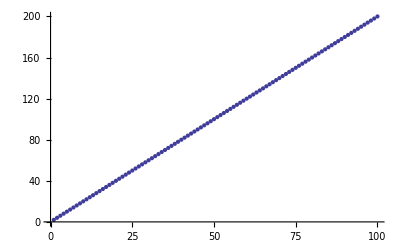

```mathematica
a[n_]:=2*n
an[l_]:=Table[a[n],{n,1,l}]
an[100]
ListPlot[an[100]]
```

{17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17}

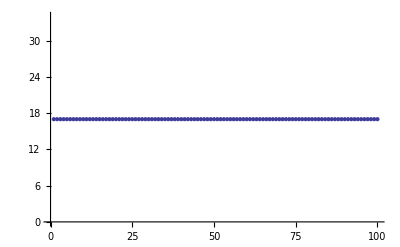

```mathematica
b[n_]:=17
bn[l_]:=Table[b[n],{n,1,l}]
bn[100]
ListPlot[bn[100]]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22,1/23,1/24,1/25,1/26,1/27,1/28,1/29,1/30,1/31,1/32,1/33,1/34,1/35,1/36,1/37,1/38,1/39,1/40,1/41,1/42,1/43,1/44,1/45,1/46,1/47,1/48,1/49,1/50,1/51,1/52,1/53,1/54,1/55,1/56,1/57,1/58,1/59,1/60,1/61,1/62,1/63,1/64,1/65,1/66,1/67,1/68,1/69,1/70,1/71,1/72,1/73,1/74,1/75,1/76,1/77,1/78,1/79,1/80,1/81,1/82,1/83,1/84,1/85,1/86,1/87,1/88,1/89,1/90,1/91,1/92,1/93,1/94,1/95,1/96,1/97,1/98,1/99,1/100}

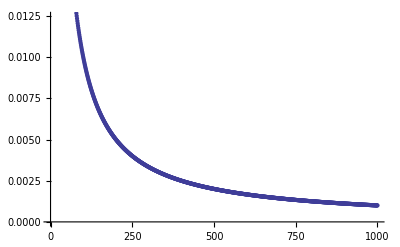

```mathematica
c[n_]:=1/n
cn[l_]:=Table[c[n],{n,1,l}]
cn[100]
ListPlot[cn[1000]]
```